# rydberg-rydberg interactions

P. Huft

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\gothr\Documents\Graduate Research\Mathematica

## single Rydberg state

### algebra

Single atom dipole matrix elements to be computed with PairInteraction module in python.

Single atom structure: include two ground states, intermediate excited state, Rydberg state. Assume that large Zeeman shifts isolate an effective 4 level lambda system.

Matrix elems. reshape H into atoms*states x atoms*states. 
H_(4 atomi - statei+1,4atomj-statej+1)=Δ_g1 δ_ij δ_(statei,1)δ_(statej,1)+Δ_g2 δ_ij δ_(statei,2)δ_(statej,2)+Δ_e δ_ij δ_(statei,3)δ_(statej,3)+ℏΩ_(1A)(δ_ij δ_(statei,2)δ_(statej,3)+δ_ij δ_(statei,3)δ_(statej,2))/2+ℏΩ_(1B)(δ_ij δ_(statei,1)δ_(statej,3)+δ_ij δ_(statei,3)δ_(statej,1))/2+ℏΩ_2(δ_ij δ_(statei,3)δ_(statej,4)+δ_ij δ_(statei,4)δ_(statej,3))/2+ (1-δ_ij)δ_(statei,4)δ_(statej,4)Vdd
Computationally more friendly to define a matrix Hij that describes the energy levels and coupling scheme of atom i, plus the interactions to atom j. Then just build Hfull by iterating over Hfull and plopping in Hij at each section atom x atom section.hmmm this is mixing a single atom basis with a two-atom basis... doesn’t really make sense as framed.

```mathematica
Hi =({{0, 0, Ω1B, 0}, {0, Δg1, Ω1A, 0}, {Ω1B*, Ω1A*, Δe1, Ω2}, {0, 0, Ω2*, Δr}});
```

test building the hamiltonian with kronecker products using only two-level systems

```mathematica
H1=({{0, Ω1/2}, {Ω1/2, Δ1}});
H2=({{0, Ω2/2}, {Ω2/2, Δ2}});
H12 =KroneckerProduct[IdentityMatrix[2],H1] + KroneckerProduct[H2,IdentityMatrix[2]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0
Ω1/2 | Δ1 | 0 | Ω2/2
Ω2/2 | 0 | Δ2 | Ω1/2
0 | Ω2/2 | Ω1/2 | Δ1+Δ2)

Now three atoms:

```mathematica
H3=({{0, Ω3/2}, {Ω3/2, Δ3}});
KroneckerProduct[IdentityMatrix[2],H12] + KroneckerProduct[H3,IdentityMatrix[4]];
%//MatrixForm
```

(0 | Ω1/2 | Ω2/2 | 0 | Ω3/2 | 0 | 0 | 0
Ω1/2 | Δ1 | 0 | Ω2/2 | 0 | Ω3/2 | 0 | 0
Ω2/2 | 0 | Δ2 | Ω1/2 | 0 | 0 | Ω3/2 | 0
0 | Ω2/2 | Ω1/2 | Δ1+Δ2 | 0 | 0 | 0 | Ω3/2
Ω3/2 | 0 | 0 | 0 | Δ3 | Ω1/2 | Ω2/2 | 0
0 | Ω3/2 | 0 | 0 | Ω1/2 | Δ1+Δ3 | 0 | Ω2/2
0 | 0 | Ω3/2 | 0 | Ω2/2 | 0 | Δ2+Δ3 | Ω1/2
0 | 0 | 0 | Ω3/2 | 0 | Ω2/2 | Ω1/2 | Δ1+Δ2+Δ3)

What is the basis of this Hamiltonian?
{123g,1e,2e,12e,3e,13e,23e,123e}
The singly-excited state is given by (1/√3){0,1,1,0,1,0,0,0}

### rabi flopping

```mathematica
(*constants*)
ℏ=1;
ee= 1.602*^-19;
c = 3*10^8;
μ0 =4π*10^-7;
ϵ0 = 1/√(c μ0);
qq = ee^2/(4 π ϵ0);
```

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω,Δ];
numStates=2; (*single atom states*)
numAtoms = 2;
H1=({{0, Ω/2}, {Ω/2, Δ}});(*assume real Rabi freq.*)
H2int = ConstantArray[0,{numAtoms numStates,numAtoms numStates}];
H2int[[numAtoms numStates,numAtoms numStates]]=ΩB; (*interaction Hamiltonian*)
```

```mathematica
H12 =KroneckerProduct[IdentityMatrix[numStates],H1]+KroneckerProduct[H1,IdentityMatrix[numStates]];
H12//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ)

```mathematica
H12+H2int//MatrixForm
```

(0 | Ω/2 | Ω/2 | 0
Ω/2 | Δ | 0 | Ω/2
Ω/2 | 0 | Δ | Ω/2
0 | Ω/2 | Ω/2 | 2 Δ+ΩB)

```mathematica
(*Build the initial array state and eqs to solve*)
Ω=2π;
Δ=0;
ΩB=20Ω;
hamiltonian = H12+Hint;
ψ = Array[Subscript[P, #][t]&,numAtoms numStates];
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<numAtoms numStates+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,ψ0,sys};
tmax=3;
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
```

Time to run sim: 0 mins

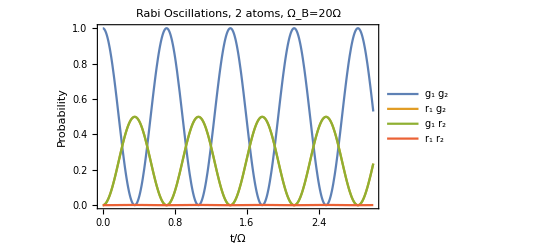

plot_rabi_flop_2atoms_2states_blockaded20.png

```mathematica
leg = {"g_1 g_2","r_1 g_2","g_1 r_2","r_1 r_2"};
plt=Plot[Evaluate[Abs[soln]^2],{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Rabi Oscillations, `` atoms, Ω_B=``Ω",numAtoms,ΩB/Ω],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
Export[ToString[StringForm["plot_rabi_flop_``atoms_``states_blockaded``.png",numAtoms,numStates,ΩB/Ω]],plt]
```

## misc testing

```mathematica
(*system params*)
numStates =4; (*single atom states*) 
numAtoms = 2;
dim = numStates*numAtoms;
Ω1A; 
Ω1B;
Ω2;
Vdd;
(*build the hamiltonian in a generalizable way for more atoms*)
Hfull = ConstantArray[0,{dim,dim}]
For[atomi=1,atomi<numAtoms+1,atomi++,
For[atomj=1,atomj<numAtoms+1,atomj++,
For[statei=1,statei<numStates+1,statei++,
For[statej=1,statej<numStates+1,statej++,
Hfull[[numStates atomi - statei+1,numStates atomj - statej+1]]=
]
]
]
]
```